```mathematica
MyZeta[k_]:=ZetaFunctionFromFormula[ListofVars[allGraphs5[k,"colofour"]]]
```

```mathematica
MyZetag[k_]:=ZetaFunctionFromFormula[ListofVars[allGraphs5[k,"colofourgenerator"]]]
```

```mathematica
Algo47[n_]:=MatrixPlot[MyZeta[n]]->Map[Labeled[MatrixPlot[MyZeta[#[[1]]]+MyZeta[#[[2]]]],#]&,allGraphs5[n,"children"]]
```

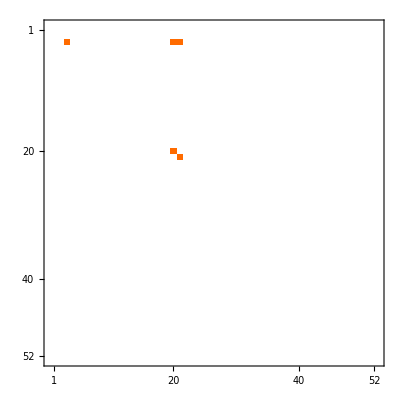
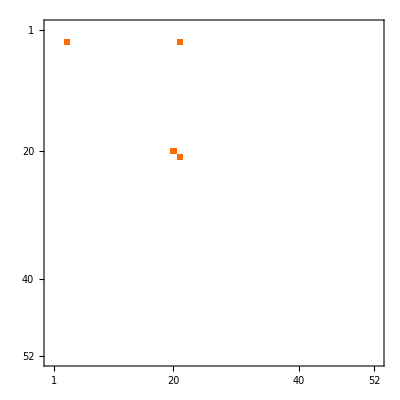
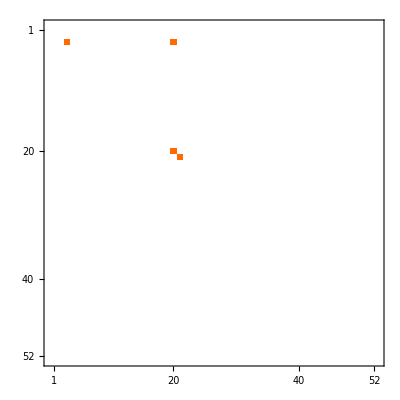
-Graphics-→{-Graphics-,-Graphics-}

```mathematica
Algo47[alfaKey]
```

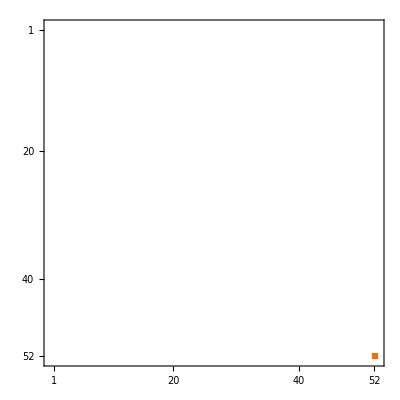

```mathematica
MyZetag[0]//MatrixPlot
```

```mathematica
Algo47g[n_]:=MatrixPlot[MyZetag[n]]->Map[Labeled[MatrixPlot[MyZetag[#[[1]]]+MyZetag[#[[2]]]],#]&,allGraphs5[n,"children"]]
```

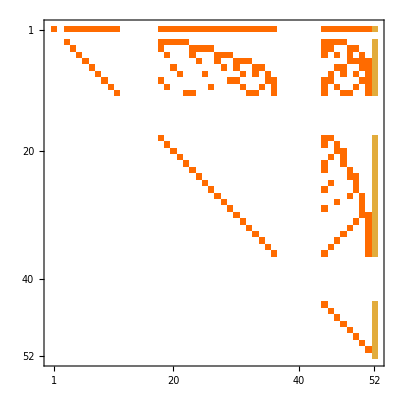
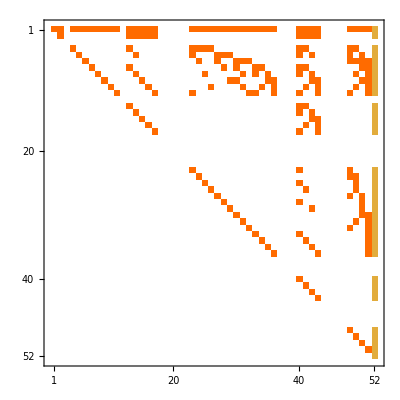
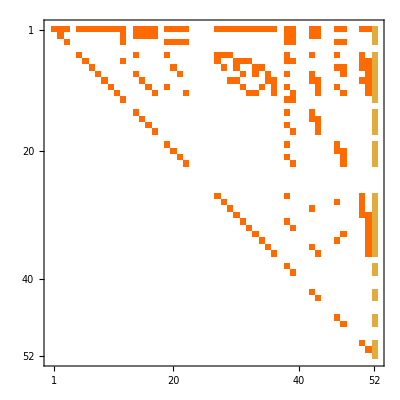
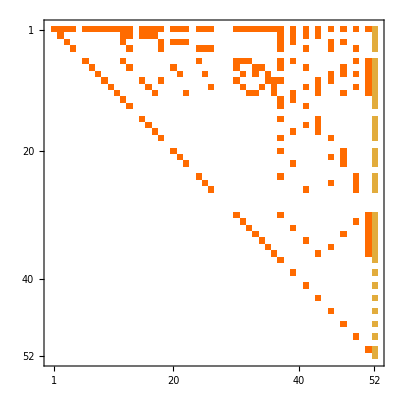
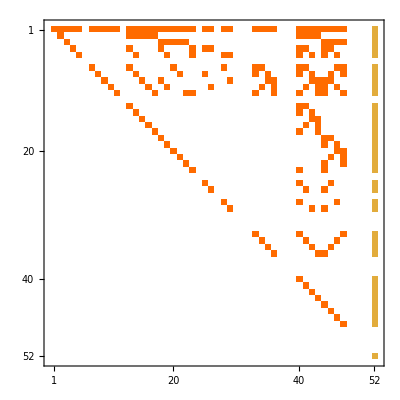
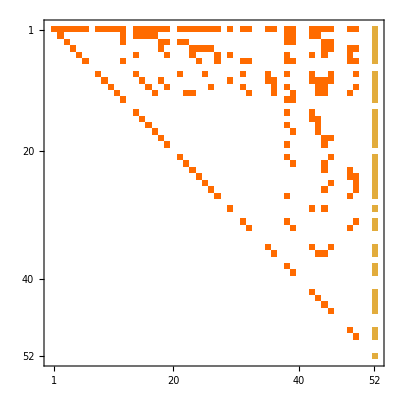
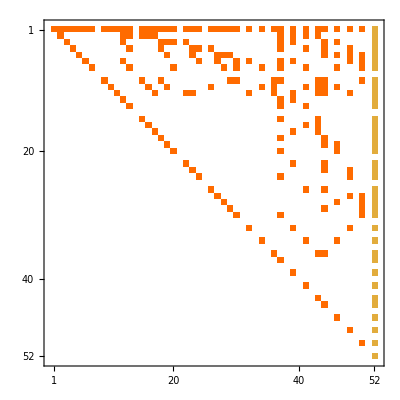
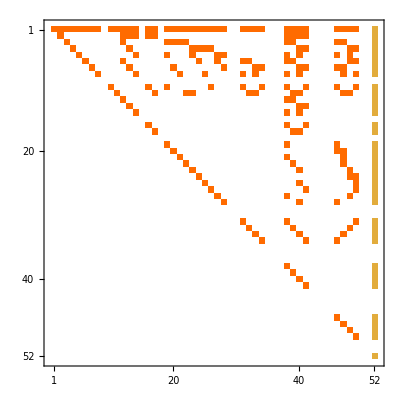
-Graphics-→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Algo47g[0]
```

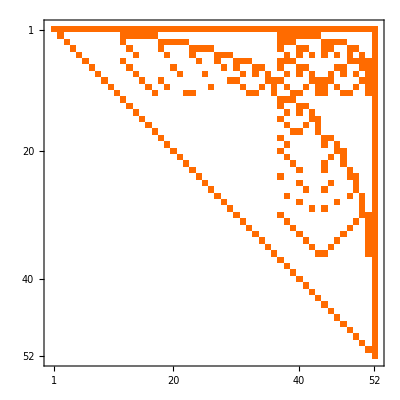
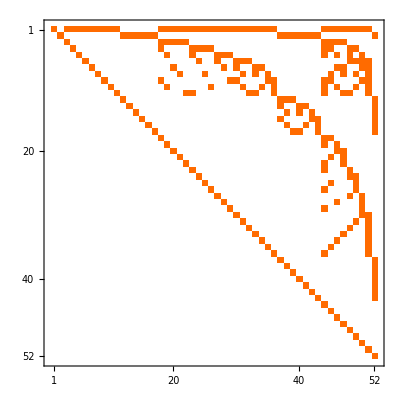
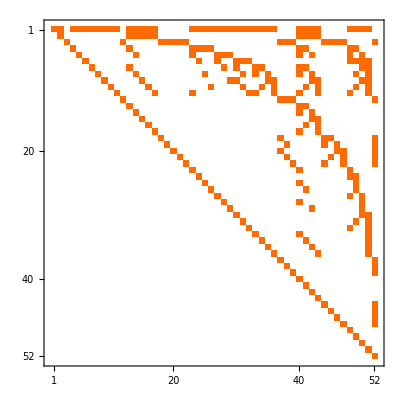
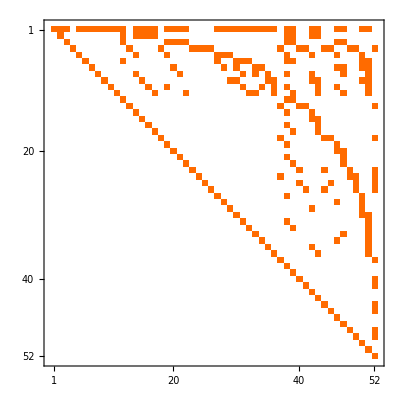
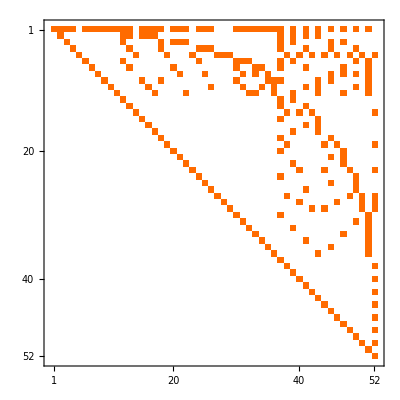
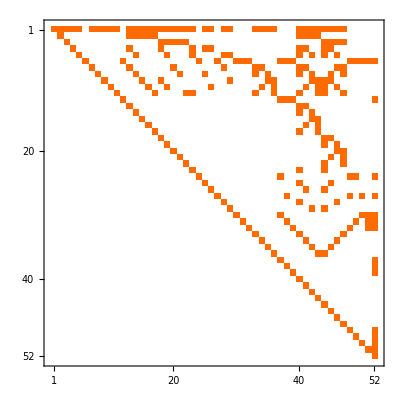
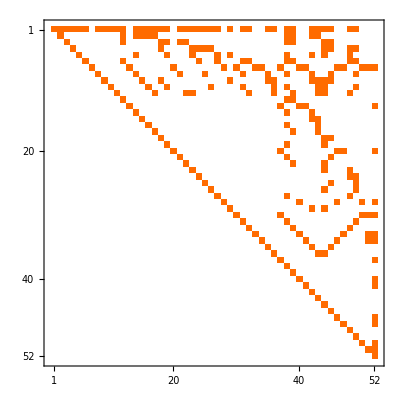
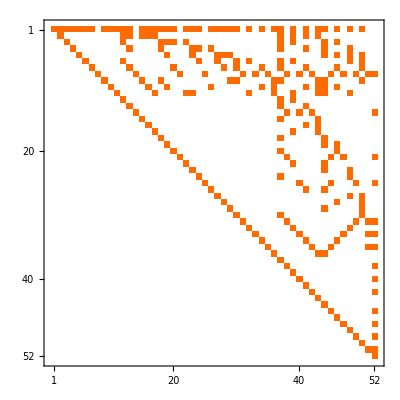
-Graphics-→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Algo47[0]
```

```mathematica
Algo48[n_]:=MatrixPlot[MyZeta[n]]->MatrixPlot[Total[Map[MyZeta[#[[1]]]+MyZeta[#[[2]]]&,allGraphs5[n,"children"]]]]
```

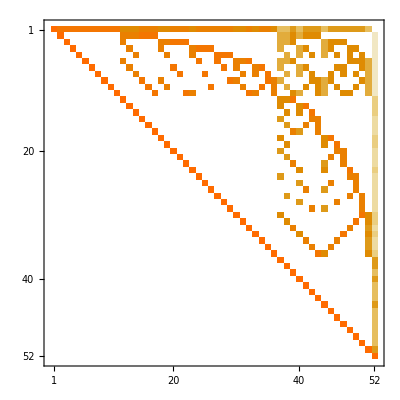
-Graphics-→-Graphics-

```mathematica
Algo48[0]
```